# Sun 2D Spectrum Calculation

An extension of the 1D Sun Spectrum (Eγ vs dNγ/dEγ ) to 2D. Previously in SUN1D (16) PRSTAB 12, 062801 (2009) the vertical emittance effect is neglected, as storage ring beams are used. ERL’s use circular beams so a 2D calculation is required, this is also needed to benchmark an improvement (relating to when source size and collimator size are similar) to ICCS3D by Balsa Terzic. The 2D model uses (3.18) of C. Sun’s thesis (also found in (A8) PRSTAB 14, 044701 (2011)). The polarisation term is negligible for the case where the polarisation is in the x-axis of the scattering plane (my answer) or we can notice the term vanishes as θ_f goes to zero, i.e. in the forward direction. This means you can just drop the term entirely and it won’t make much difference in the final result (Geoff’s answer).

Potential Error Sources
• σ_k is never defined in Sun’s thesis - the specific form I have used here may be wrong. Potentially Check Siegmann Laser book to see exact definition. Not used in Siegmann laser book, convinced myself that I am using the correct definition though as derived Δk/kand used in form that matches σ_E_e usage and both are rms energy spreads.
• The integral over k goes from ∞ to 0 to sum over all modes (confirmed by Geoff) in the laser but its impractical. Implemented k ± 3Δk to just go for the fundamental harmonic + a bandwidth. Would need convergence testing
• Terms such as N_laser and z_R which are outside the integration are actually dependent on λ and therefore k. I can understand N_Laser as it is taking the average and it is invariant but z_R seems more spurious. z_R is held constant throughout currently. (Geoff says taking these as constant is the best approximation we can do).
• Currently the code does not take the laser bandwidth variation into account with the cross section, whilst this is predicted to be a small effect it is still not a full treatment of laser energy spread. In practice this means that EL is kept constant during integration. Maybe this full treatment could be added though?

## Units, Constants and Cases

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
μm=10^-6;
```

```mathematica
(*Units*)
phkeVnC=(keV*nC)/elecharge;
```

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Cases - CBETA 150MeV 0.5% BW*)
CBETA150={Ee->150MeV,Q->32pC,Epulse->62μJ,λ->1064nm,θcol->0.43333mrad,ϕ->0,ϵnx->0.3mm mrad,βx->0.126176,ϵny->0.3mm mrad,βy->0.126176,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,dEγ->200};
```

dEγ is the energy step in eV between each sampled point in the distribution in eV, Ee is the kinetic energy of the electron beam. Δk is the laser wavenumber spread (just laser energy spread as proportional).

```mathematica
trialcase=CBETA150;
```

## Polarisation

The polarisation term is negligible for the case where the polarisation is in the x-axis of the scattering plane (my answer) or we can notice the term vanishes at θ_f goes to zero, i.e. in the forward direction. This means you can just drop the term entirely and it won’t make much difference in the final result (Geoff’s answer). By this line of reasoning we can set τ, the azimuthal angle of the linear polarisation P_t with respect to the x_eaxis to zero and set ϕ_f, the azimuthal angle of the scattering plane to zero. τ = 0 , ϕ_f =0

```mathematica
τ=0;
ϕf=0;
```

## Scattered Photon Energy Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ;(*in eV, hbar is in eV, 2π due to hbar*)
```

EL is the energy of the incident photon in eV. EL is independent of k, this is currently used for the “averaged” values of N_L and z_R and also used in the “averaged” cross section terms.

## Scattered Photon Energy

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
Eγset[λ,Ee,ϕ,θcol]/.trialcase
```

396834.

## Sun Preliminaries

```mathematica
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/(β[Ee]*γ[Ee]);
ϵy[Ee_,ϵny_]:=ϵny/(β[Ee]*γ[Ee]);
zr[λ_,σL_]:=(4*π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee;
klaser[λ_]:=(2π)/λ;
σk[Δk_,λ_]:=Δk*klaser[λ];
```

The σ_k term usage here could be wrong. It is undefined in Sun’s works, it has been assumed to mirror the form used for the electron bunch energy spread.

## Collimation

```mathematica
R[L_,θcol_]:=L*θcol;(*Far field collimation, small angle approximation*)
```

```mathematica
(*Circular Collimation*)
x0[L_,θcol_]:=R[L,θcol];
y0[L_,θcol_,xd_]:=Re[Sqrt[R[L,θcol]^2-xd^2]];
(*Square Collimation*)
(*x0[A_]:=A;
y0[B_]:=B;*)
```

Square aperture created in two dimensions (x_0= A for x_d, y_0=B for x_d), Circular aperture based on the radius (x_0=R for x_d, y_0= Re Sqrt[R^2 - x_d^2] for y_d or vice versa depending on order of integration).

## Sun Intermediaries

Here we assume collisions are done at a waist i.e α_x=α_y= 0. Therefore, the ξ_(x/y) formula are simplified from Sun’s thesis.

```mathematica
γbar[λ_,Eγ_,θx_,θy_]:=(2*Eγ*EL[λ])/(me*(4*EL[λ]-Eγ*(θx^2+θy^2)))*(1+Sqrt[1+((4*EL[λ]-Eγ*(θx^2+θy^2))*me^2)/(4*EL[λ]^2*Eγ)]);
ξx[βx_,L_,k_,Ee_,ϵnx_,λ_,σL_]:=1+(βx/L)^2+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ξy[βy_,L_,k_,Ee_,ϵny_,λ_,σL_]:=1+(βy/L)^2+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
ζx[k_,βx_,Ee_,ϵnx_,λ_,σL_]:=1+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζy[k_,βy_,Ee_,ϵny_,λ_,σL_]:=1+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,k_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,k,Ee,ϵnx,λ,σL])/(βx*ζx[k,βx,Ee,ϵnx,λ,σL])];
σθy[Ee_,ϵny_,βy_,L_,k_,λ_,σL_]:=Sqrt[(ϵy[Ee,ϵny]*ξy[βy,L,k,Ee,ϵny,λ,σL])/(βy*ζy[k,βy,Ee,ϵny,λ,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θymax[λ_,Eγ_]:=Sqrt[(4*EL[λ])/Eγ];
θxmax[λ_,Eγ_,θy_]:=Sqrt[(4*EL[λ])/Eγ-θy^2];
```

The limits of integration have both been constructed using EL i.e the constant case. I’m unsure whether this is correct? Feels slightly incorrect, but simpler to get code running like this.

```mathematica
kmin[λ_,Δk_]:=klaser[λ]*(1-3*Δk);
kmax[λ_,Δk_]:=klaser[λ]*(1+3*Δk);
```

## Prefactor

```mathematica
prefactor[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_]:=(re^2*Ne[Q]*NL[Epulse,λ])/(4*π^3*hbar*clight*zr[λ,σL]*σγ[ΔEe,Ee]*σk[Δk,λ]*L^2);
```

```mathematica
prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]/.trialcase//ScientificForm
```

5.12004×10^-5

## Separated Integral Terms

```mathematica
term1[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_]:=1/(Sqrt[ζx[k,βx,Ee,ϵnx,λ,σL]*ζy[k,βy,Ee,ϵny,λ,σL]]*σθx[Ee,ϵnx,βx,L,k,λ,σL]*σθy[Ee,ϵny,βy,L,k,λ,σL]);
```

```mathematica
term2[λ_,Eγ_,θx_,θy_]:=γbar[λ,Eγ,θx,θy]/(1+(2*γbar[λ,Eγ,θx,θy]*EL[λ])/me);
```

```mathematica
term3[λ_,Eγ_,θx_,θy_,τ_,ϕf_]:=(1/4*((4*γbar[λ,Eγ,θx,θy]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))+(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))/(4*γbar[λ,Eγ,θx,θy]^2*EL[λ]))-2*Cos[τ-ϕf]^2*(γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))/((1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))^2));
```

```mathematica
term4[θx_,xd_,L_,Ee_,ϵnx_,βx_,k_,λ_,θy_,yd_,ϵny_,βy_,Eγ_,ΔEe_,Δk_,σL_]:=Exp[-(θx-xd/L)^2/(2*σθx[Ee,ϵnx,βx,L,k,λ,σL]^2)-(θy-yd/L)^2/(2*σθy[Ee,ϵny,βy,L,k,λ,σL]^2)-(γbar[λ,Eγ,θx,θy]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)-(k-klaser[λ])^2/(2*σk[Δk,λ]^2)];
```

## Integral Term

```mathematica
intterm[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,θx_,θy_,τ_,ϕf_,xd_,yd_,ΔEe_,Δk_]:=term1[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL]*term2[λ,Eγ,θx,θy]*term3[λ,Eγ,θx,θy,τ,ϕf]*term4[θx,xd,L,Ee,ϵnx,βx,k,λ,θy,yd,ϵny,βy,Eγ,ΔEe,Δk,σL]
```

```mathematica
INTterm[βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,τ_,ϕf_,ΔEe_,Δk_]:=NIntegrate[intterm[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,θx,θy,τ,ϕf,xd,yd,ΔEe,Δk]/.trialcase,{xd,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yd,-y0[L,θcol,xd]/.trialcase,y0[L,θcol,xd]/.trialcase},{θy,-θymax[λ,Eγ]/.trialcase,θymax[λ,Eγ]/.trialcase},{θx,-θxmax[λ,Eγ,θy]/.trialcase,θxmax[λ,Eγ,θy]/.trialcase},{k,kmin[λ,Δk]/.trialcase,kmax[λ,Δk]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->40000000}];
```

## Spectral Density Calculation

```mathematica
dNdEγ[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_,βx_,ϵnx_,βy_,ϵny_,Eγ_,τ_,ϕf_]:=prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]*INTterm[βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,τ,ϕf,ΔEe,Δk];
```

```mathematica
SpecDen=Table[{Eγ/keV,phkeVnC/((Q/.trialcase)/elecharge)*dNdEγ[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L,βx,ϵnx,βy,ϵny,Eγ,τ,ϕf]/.trialcase},{Eγ,Eγset[λ,Ee*(1-15*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,dEγ/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 30915610 integrand evaluations. NIntegrate obtained 1.51713 and 0.0360461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 30915610 integrand evaluations. NIntegrate obtained 1.74088 and 0.0412345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 30915610 integrand evaluations. NIntegrate obtained 1.98557 and 0.0467702 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Get["GetNameFunction"]; 
SpeakName;
```

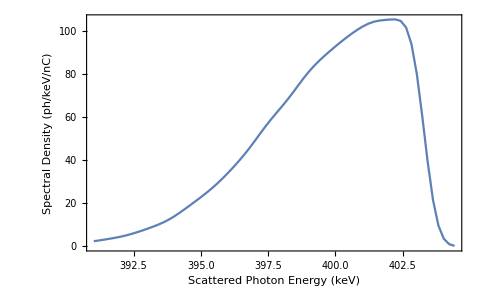

```mathematica
ListLinePlot[SpecDen,Frame->True,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density (ph/keV/nC)"},PlotRange->Full]
```

## Spectral Density Per Electron

```mathematica
SpecDenElectron=Partition[Riffle[SpecDen⟦All,1⟧,SpecDen⟦All,2⟧/phkeVnC],2];
```

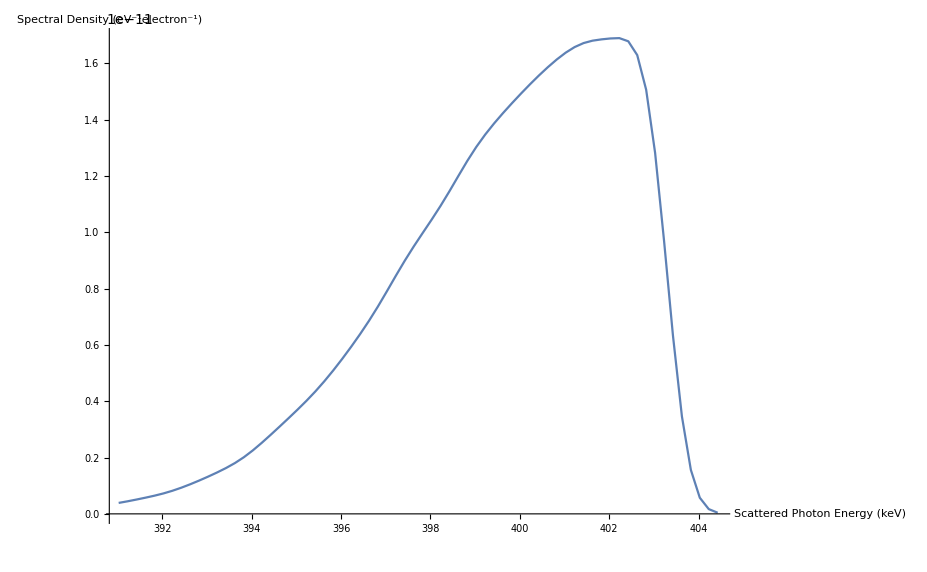

```mathematica
ListLinePlot[SpecDenElectron,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (eV^-1electron^-1)"},PlotRange->Full]
```

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/SUN2D_results"];
SpecDen>>"CBETA150_40mil.txt";
SpecDenElectron>>"CBETA150e-_40mil.txt";
```

# SUN 2D Benchmarking

## Plotting Functions

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Benchmarking of No. Points in QuasiMonteCarloIntegration

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/SUN2D_results"];
```

```mathematica
CBETA150mil05=<<"CBETA150_0.5mil.txt";
CBETA150mil1=<<"CBETA150_1mil.txt";
CBETA150mil5=<<"CBETA150_5mil.txt";
CBETA150mil10=<<"CBETA150_10mil.txt";
CBETA150mil15=<<"CBETA150_15mil.txt";
CBETA150mil20=<<"CBETA150_20mil.txt";
CBETA150mil30=<<"CBETA150_30mil.txt";
CBETA150mil40=<<"CBETA150_40mil.txt";
CBETA150mil50=<<"CBETA150_50mil.txt";
CBETA150mil100=<<"CBETA150_100mil.txt";
```

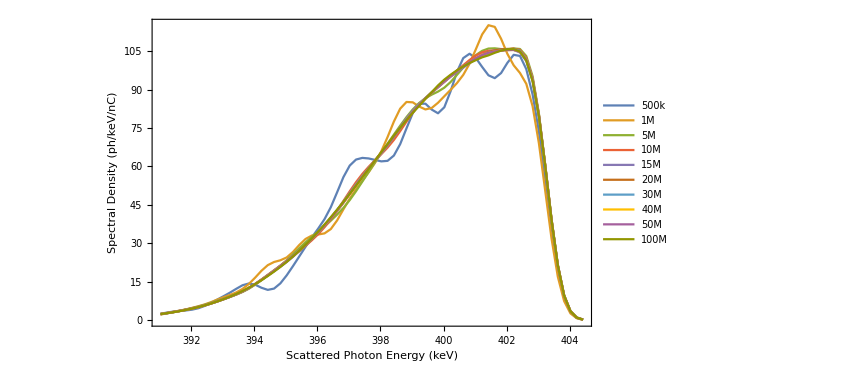

```mathematica
ListLinePlot[{CBETA150mil05,CBETA150mil1,CBETA150mil5,CBETA150mil10,CBETA150mil15,CBETA150mil20,CBETA150mil30,CBETA150mil40,CBETA150mil50,CBETA150mil100},Frame->True,LabelStyle->15,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density (ph/keV/nC)"},PlotRange->Full,PlotLegends->Placed[LineLegend[{"500k","1M","5M","10M","15M","20M","30M","40M","50M","100M"},LabelStyle->12,LegendFunction->frame],{0.15,0.75}]]
```

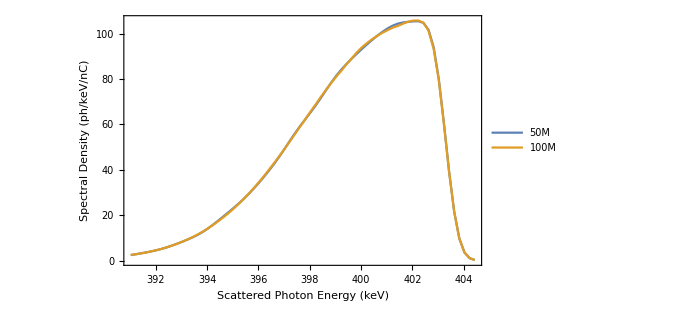

```mathematica
ListLinePlot[{CBETA150mil50,CBETA150mil100},Frame->True,LabelStyle->15,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density (ph/keV/nC)"},PlotRange->Full,PlotLegends->Placed[LineLegend[{"50M","100M"},LabelStyle->12,LegendFunction->frame],{0.15,0.8}]]
```

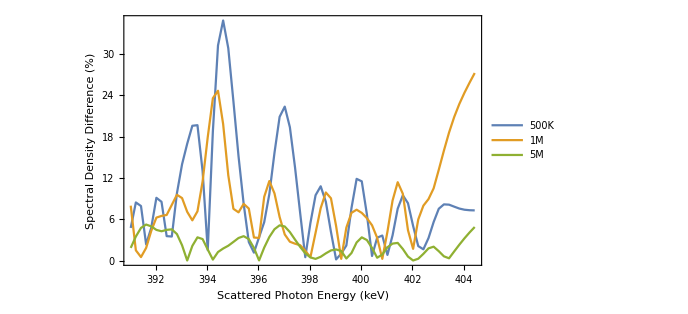

```mathematica
ListLinePlot[{Partition[Riffle[CBETA150mil05⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil05⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil1⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil1⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil5⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil5⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2]},Frame->True,LabelStyle->15,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density Difference (%)"},PlotRange->Full,PlotLegends->Placed[LineLegend[{"500K","1M","5M"},LabelStyle->12,LegendFunction->frame],{0.5,0.8}]]
```

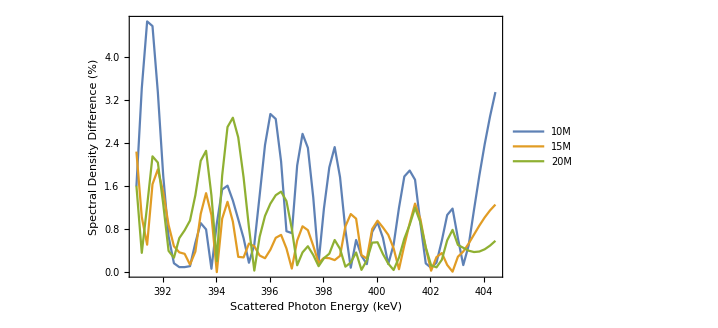

```mathematica
ListLinePlot[{Partition[Riffle[CBETA150mil10⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil10⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil15⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil15⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil20⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil20⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2]},Frame->True,LabelStyle->15,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density Difference (%)"},PlotRange->Full,PlotLegends->Placed[LineLegend[{"10M","15M","20M"},LabelStyle->12,LegendFunction->frame],{0.5,0.8}]]
```

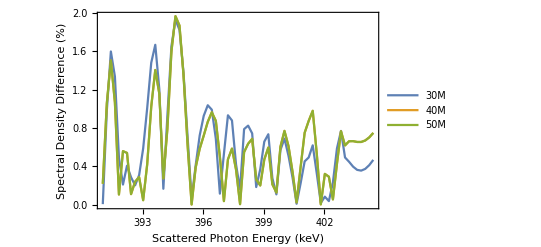

```mathematica
ListLinePlot[{Partition[Riffle[CBETA150mil30⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil30⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil40⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil40⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2],Partition[Riffle[CBETA150mil50⟦All,1⟧,Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil50⟦All,2⟧)/CBETA150mil100⟦All,2⟧]*100],2]},Frame->True,LabelStyle->15,FrameLabel->{"Scattered Photon Energy (keV)","Spectral Density Difference (%)"},PlotRange->Full,PlotLegends->Placed[LineLegend[{"30M","40M","50M"},LabelStyle->12,LegendFunction->frame],{0.5,0.8}]]
```

```mathematica
ResDat={{0.5,1,5,10,15,20,30,40,50},{Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil05⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil1⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil5⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil10⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil15⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil20⟦All,2⟧)/CBETA150mil100⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil30⟦All,2⟧)/CBETA150mil30⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil40⟦All,2⟧)/CBETA150mil40⟦All,2⟧]],Mean[Abs[(CBETA150mil100⟦All,2⟧-CBETA150mil50⟦All,2⟧)/CBETA150mil100⟦All,2⟧]]}*100};
```

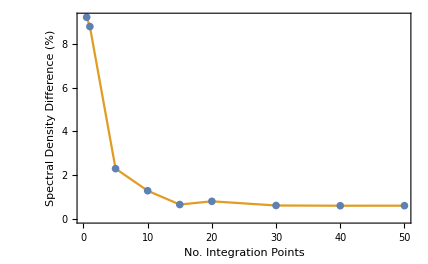

```mathematica
ListPlot[{Transpose[ResDat],Transpose[ResDat]},Joined->{False,True},Frame->True,FrameLabel->{"No. Integration Points","Spectral Density Difference (%)"}]
```